## The Potential

```mathematica
(* Following the notes of Dr. P. Zimmerman the Schrodinger equation/liouville normal form of the spin spheroidal equation defined by the potential *)
```

```mathematica
V[x_]:=Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2+I √2 ℏ s Sin[x]
```

```mathematica
(* Q: where are the harmonic minima of the classical part of the potential? *)
```

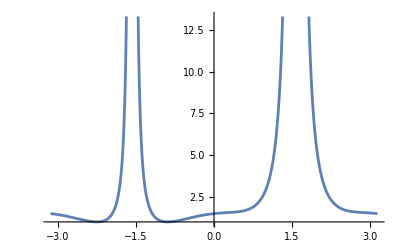

```mathematica
Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2/.{μ0->1/2,μ1->1/3},{x,-π,π}]
```

```mathematica
(*  |μ1|<μ0&&  *)
```

```mathematica
(* Some interesting regions of parameter space should be identified...   *)
Manipulate[Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,{x,-2π,2π}],{μ0,-2,2},{μ1,-2,2}]
```

```mathematica
Show[
Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,{x,-2π,2π}],ListPlot[HarmonicMinima[μ0,μ1,1]]
]
```

```mathematica
Manipulate[
Show[
Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,{x,-2π,2π}],ListPlot[HarmonicMinima[μ0,μ1,1]]
],
{μ0,-2,2},{μ1,-2,2}]
```

### check Liouville normal form

```mathematica
D[Sin[θ]D[Ψ[θ]/(√Cos[θ]),θ],θ]//FullSimplify
```

((13 Sin[θ]+Sin[3 θ]) Ψ[θ]+16 Cos[θ] (Ψ'[θ]+Cos[θ] Sin[θ] Ψ''[θ]))/(16 Cos[θ]^(5/2))

```mathematica
1/(√Sin[θ])D[Sin[θ]D[Ψ[θ]/(√Sin[θ]),θ],θ]//FullSimplify
```

1/4 (2+Cot[θ]^2) Ψ[θ]+Ψ''[θ]

```mathematica
1/4 (2+Cot[θ]^2) -1/4-1/4 Csc[θ]^2//FullSimplify
```

0

```mathematica
Sin[θ]/(√Sin[θ])(k-(m^2+s^2+2m s Cos[θ])/Sin[θ]^2-c^2 Sin[θ]^2-2c s Cos[θ])Ψ[θ]/(√Sin[θ])+(1/4+1/4 Csc[θ]^2 )Ψ[θ]//FullSimplify
```

(1/4+k-2 c s Cos[θ]-1/4 (-1+4 m^2+4 s^2+8 m s Cos[θ]) Csc[θ]^2-c^2 Sin[θ]^2) Ψ[θ]

```mathematica
μ1/(1-Cos[θ])+μ2/(1+Cos[θ])//Together//FullSimplify
```

(μ1+μ2+(μ1-μ2) Cos[θ]) Csc[θ]^2

```mathematica
(1/4+k-2 c s Cos[θ]-1/4 (-1+4 m^2+4 s^2+8 m s Cos[θ]) Csc[θ]^2-c^2 Sin[θ]^2) /.θ->x-π/2//FullSimplify
```

1/4+k-c^2 Cos[x]^2-2 c s Sin[x]-1/4 Sec[x]^2 (-1+4 m^2+4 s^2+8 m s Sin[x])

## Find the Harmonic Minima

```mathematica
Clear[roots]
```

```mathematica
roots=x/.Solve[D[Cos[x]^2+(m0+m1 Sin[x])/Cos[x]^2,x]==0,x]//FullSimplify;
```

```mathematica
(* define a function that finds harmonic minima give the parameters μ0,μ1 of the potential. *)
(* M determines the number of minima  *)
(* {x,E} outputs the x coord of the minima and the energy E it corresponds to *)
HarmonicMinima[μ0_,μ1_,M_]:=Module[{rs,test,ddV},
rs=roots/.{m1->μ1,m0->μ0};
rs=N[Flatten[Table[rs/.C[1]->n,{n,-M,M}]],2000]//DeleteCases[#,_Complex]&//DeleteDuplicates;
rs={#,Limit[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,x->#]}&/@(rs);
ddV=D[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,x,x];
test=If[Limit[ddV,x->#[[1]]]>0,True,False]&;
rs=Select[rs,test]
]
```

```mathematica
HarmonicMinima[1,1,1]//N
```

{{-7.85398,0.5},{-1.5708,0.5},{4.71239,0.5}}

```mathematica
HarmonicMinima[2,2,1]//N
```

{{-7.85398,1.},{-1.5708,1.},{4.71239,1.}}

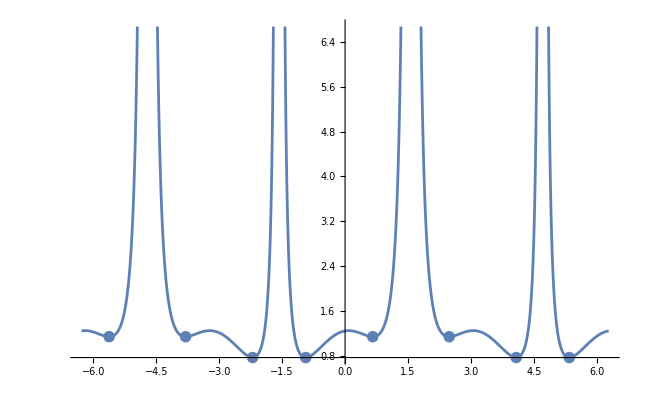

```mathematica
Module[{μ0,μ1,rs,test,ddV},
μ0=1/4;
μ1=1/8;
Show[
Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,{x,-2π,2π}],ListPlot[HarmonicMinima[μ0,μ1,1]]
]]
```

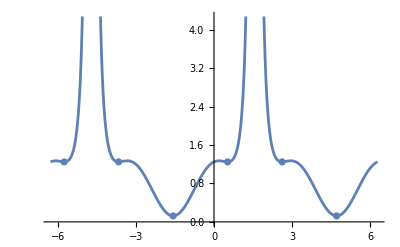

```mathematica
Module[{μ0,μ1,rs,test,ddV},
μ0=1/4;
μ1=1/4;
Show[
Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,{x,-2π,2π}],ListPlot[HarmonicMinima[μ0,μ1,1]]
]]
```

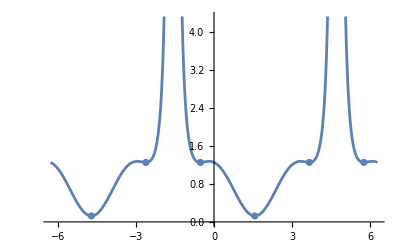

```mathematica
Module[{μ0,μ1,rs,test,ddV},
μ0=1/4;
μ1=-1/4;
Show[
Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2,{x,-2π,2π}],ListPlot[HarmonicMinima[μ0,μ1,1]]
]]
```

## Mapping the Regions Of the potential

```mathematica
(* the potential mapped to the algebraic curve *)
(* remove μ2 terms *)
1-u+(-2+u) x^2+x^4+μ0-x^3 μ2+x (μ1+μ2)/.μ2->0
```

1-u+(-2+u) x^2+x^4+μ0+x μ1

```mathematica
Discriminant[v[x],x]//FullSimplify
```

-16 (u^2-4 μ0)^2 (-1+u-μ0)-4 (-2+u) (u (32+u)-4 (8+9 μ0)) μ1^2-27 μ1^4

```mathematica
v[x_]:=1-u+(-2+u) x^2+x^4+μ0+x μ1
```

```mathematica
Manipulate[ContourPlot[-y^2==1-u+(-2+u) x^2+x^4+μ0+x μ1,{x,-8,8},{y,-12,12}],{u,-2,2},{μ0,-2,2},{μ1,-2,2}]
```

```mathematica
D[v[x],x]
```

0==2 (-2+u) x+4 x^3+μ1

```mathematica
(* Sturm sequence *)
p[0]=v[x];
p[1]=D[v[x],x];
p[2]=-PolynomialRemainder[v[x],D[v[x],x],x]//FullSimplify;
p[3]=-PolynomialRemainder[p[1],p[2],x]//FullSimplify;
p[4]=-PolynomialRemainder[p[2],p[3],x]//FullSimplify;
```

```mathematica
Coefficient[p[3],x]//FullSimplify
```

-(2 (-2+u) (u^2-4 μ0)+9 μ1^2)/(-2+u)^2

```mathematica
CoefficientList[p[0],x]//Last
CoefficientList[p[1],x]//Last
CoefficientList[p[2],x]//Last
Factor[CoefficientList[p[3],x]//Last]
Factor[CoefficientList[p[4],x]//Last]
```

1

4

1-u/2

-(-4 u^2+2 u^3+16 μ0-8 u μ0+9 μ1^2)/(-2+u)^2

-(((-2+u)^2 (-16 u^4+16 u^5+128 u^2 μ0-128 u^3 μ0-16 u^4 μ0-256 μ0^2+256 u μ0^2+128 u^2 μ0^2-256 μ0^3+256 μ1^2-384 u μ1^2+120 u^2 μ1^2+4 u^3 μ1^2+288 μ0 μ1^2-144 u μ0 μ1^2+27 μ1^4))/(4 (-4 u^2+2 u^3+16 μ0-8 u μ0+9 μ1^2)^2))

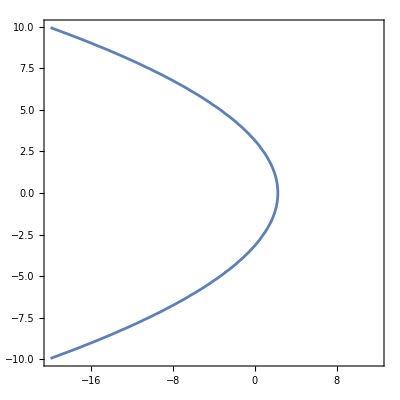

```mathematica
ContourPlot[Evaluate[0==(-4 u^2+2 u^3+16 μ0-8 u μ0+9 μ1^2)/.u->-3],{μ0,-20,12},{μ1,-10,10}]
```

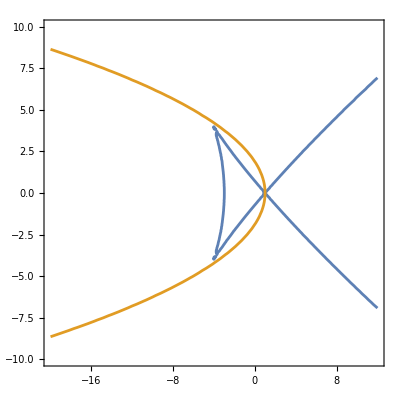

```mathematica
ContourPlot[{Evaluate[0==Discriminant[v[x],x]/.u->-2],Evaluate[0==(-4 u^2+2 u^3+16 μ0-8 u μ0+9 μ1^2)/.u->-2]},{μ0,-20,12},{μ1,-10,10}]
```

```mathematica
ContourPlot3D[Evaluate[0==Discriminant[v[x],x]],{u,-6,6},{μ0,-6,6},{μ1,-6,6}]
```

-Graphics3D-

## Raleigh-Schrodinger Perturbation theory with Bender Wu

```mathematica
(* Apply Bender Wu mathematical package to generate `high' orders of perturbation expansion for energy levels *)
(* Inputs: *)
(* μ0,μ1,s are the parameters of the potential  *)
(* l is the level number *)
(* M is the order of PT  *)

(* Outputs: *)
(* list of form {{x0,{E01,E02,...,E0M} },...,{xm,{Em1,Em2,...,EmM}}} *)
(* That is, applies BenderWu at each of the m harmonic minimum xi of the potential *)
```

```mathematica
RSPT[μ0_,μ1_,s_,l_,M_]:=Module[{mu0,mu1,tilt,x0,funcs,func,pt},
mu0=μ0;
mu1=μ1;
tilt=s;
x0=Mod[HarmonicMinima[μ0,μ1,4][[1;;,1]],2π]//N[#,1000]&//DeleteDuplicates;
funcs=Table[Normal@Series[Cos[x]^2+(mu0+mu1 Sin[x])/Cos[x]^2,{x,xi,2M+1}]/.x->x+xi,{xi,x0}];
pt=Table[BenderWu[{func,-I tilt √2 Sin[x-x0[[1]]]},x,l,M,Output->"Energy",Monitor->False],{func,funcs}];
Table[{x0[[i]],pt[[i]]},{i,Length[x0]}]
]
```

```mathematica
Etest=RSPT[1/4,-1/8,I/100,2,40];
```

```mathematica
HarmonicMinima[1/4,-1/8,1][[1;;,1]]//N
```

{-4.07994,-5.34484,-8.76546,-6.9425,2.20325,0.938343,-2.48228,-0.659315,8.48644,7.22153,3.80091,5.62387}

## Large order Analysis

```mathematica
El = Gamma[n]/s^n
```

```mathematica
(* defines richardson acceleration of the sequence {f[1],f[2],f[3],...} of order O evaluated at the nth element of Subscript[R, O][f](n) *)
Rich[f_,O_,n_]:=Sum[(f[n+k](n+k)^O(-1)^(k+O))/(k!(O-k)!),{k,0,O}]
(* calculates tunneling action from ratio of successive terms of the perturbative series. Uses richardson of order O *)
Action[Edata_,O_]:=Module[{sc},
sc[t_]:=(t Edata[[t-1]])/Edata[[t]];
N[Rich[sc,O,Length[Edata]-O],200]
]
```

```mathematica
(* a sample calculation *)
Etest=RSPT[1/4,-1/8,0,2,70];
```

```mathematica
(* four series (two are duplicates because spin quantum correction term is set to 0) *)
(* Note the weird error in the last of the calculated terms of the series for Etest[[1..2,2]] *)
Etest[[1,2]]//N
```

{5.78767,-8.13007,-14.901,-58.6615,-312.392,-1957.98,-13635.1,-102530.,-818313.,-6.85439×10^6,-5.97855×10^7,-5.39924×10^8,-5.02723×10^9,-4.8102×10^10,-4.71759×10^11,-4.73271×10^12,-4.84856×10^13,-5.06567×10^14,-5.39128×10^15,-5.83932×10^16,-6.43119×10^17,-7.19721×10^18,-8.17892×10^19,-9.43234×10^20,-1.10326×10^22,-1.30799×10^23,-1.57083×10^24,-1.9096×10^25,-2.34806×10^26,-2.91759×10^27,-3.65943×10^28,-4.62689×10^29,-5.88727×10^30,-7.52202×10^31,-9.62232×10^32,-1.22741×10^34,-1.55206×10^35,-1.92783×10^36,-2.31612×10^37,-2.61237×10^38,-2.57568×10^39,-1.692×10^40,1.08733×10^41,7.83884×10^42,2.2585×10^44,5.29751×10^45,1.13302×10^47,2.29762×10^48,4.49245×10^49,8.52993×10^50,1.575×10^52,2.81828×10^53,4.84002×10^54,7.81156×10^55,1.12817×10^57,1.25046×10^58,1.70455×10^58,-5.0612×10^60,-2.26396×10^62,-7.42145×10^63,-2.14972×10^65,-5.81593×10^66,-1.50383×10^68,-3.75597×10^69,-9.09924×10^70,-2.1376×10^72,-4.84637×10^73,-1.04854×10^75,-2.11361×10^76,-3.7482×10^77,-6.08741×10^108}

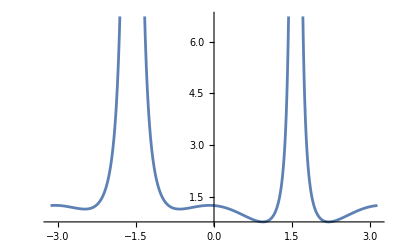

```mathematica
(* the potential in this region of parameters *)
Plot[Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2/.{μ0->1/4,μ1->-1/8},{x,-π,π}]
```

### Upper well (false vacuum)

```mathematica
(* compare the resurgent calculation from the large order behavior of PT to numeric integration for the tunneling action *)
HarmonicMinima[1/4,-1/8,0]//N
```

{{2.20325,0.776347},{0.938343,0.776347},{-2.48228,1.14747},{-0.659315,1.14747}}

```mathematica
Solve[(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2)/.{u->1.1474743949216977,μ0->1/4,μ1->-1/8})==0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2.48228},{x→-0.659315},{x→0.297527},{x→1.19988},{x→1.94172},{x→2.84407}}

```mathematica
NIntegrate[(I 2 √2 √(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2))/.{u->1.1474743949216977,μ0->1/4,μ1->-1/8}),{x,-0.6593148525805923,0.2975270819838135}]//Chop
```

-0.634914

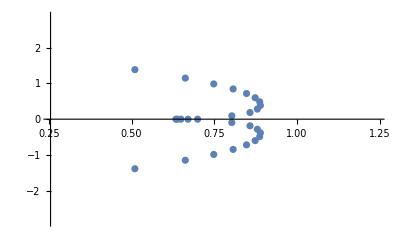

```mathematica
ListPlot[ReIm@s/.Solve[Denominator@PadeApproximant[Sum[(Etest[[3,2]][[i]])/((i)!)s^(i-1),{i,1,Length[Etest[[1,2]]]-1}],{s,0,30}]==0,s]]
```

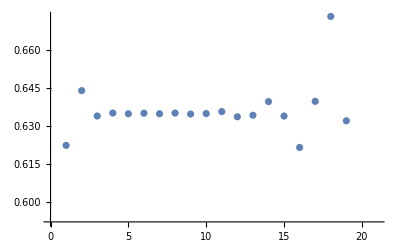

```mathematica
Table[Action[Most@(Etest[[3,2]]),o],{o,0,20}]//ListPlot
```

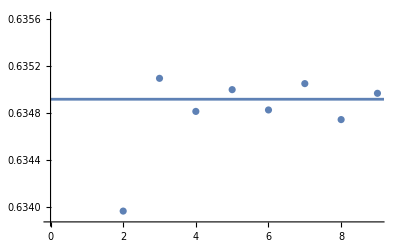

```mathematica
Show[Table[Action[Etest[[3,2]],o],{o,1,9}]//ListPlot,Plot[0.6349141232880382,{n,0,12}]]
```

### Lower well

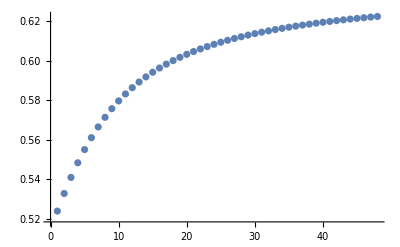

```mathematica
Table[(i Etest[[3,2,i-1]]/Etest[[3,2,i]])//N,{i,23,Length[Etest[[1,2]]]-1}]//ListPlot
```

```mathematica
(* compare the resurgent calculation from the large order behavior of PT to numeric integration for the tunneling action *)
HarmonicMinima[1/4,-1/8,0]//N
```

{{2.20325,0.776347},{0.938343,0.776347},{-2.48228,1.14747},{-0.659315,1.14747}}

```mathematica
(* the lower minima has turning points *)
Solve[(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2)/.{u->0.7763469803820997,μ0->1/4,μ1->-1/8})==0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2.30186+0.405706 ⅈ},{x→-2.30186-0.405706 ⅈ},{x→-0.839734-0.405706 ⅈ},{x→-0.839734+0.405706 ⅈ},{x→0.938343},{x→2.20325}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

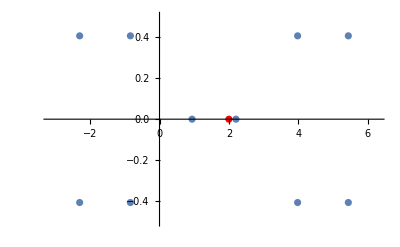

```mathematica
(* in the complex plane*)
Show[ReIm@x/.Solve[(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2)/.{u->0.7763469803820997,μ0->1/4,μ1->-1/8})==0]//ListPlot[#,PlotRange->{{-π,2π},{.5,-.5}}]&,ReIm@(x+2π)/.Solve[(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2)/.{u->0.7763469803820997,μ0->1/4,μ1->-1/8})==0]//ListPlot,ListPlot[{π/2,0},PlotStyle->Red]]
```

```mathematica
(* the tunneling action:*)
NIntegrate[(2 √2 √(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2))/.{u->0.7763469803820997,μ0->1/4,μ1->-1/8}),{x,0.9383425126045616,-0.8397344491201683+0.40570603101579517 ⅈ}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0791622+0.232165 ⅈ}. NIntegrate obtained -0.343165-0.0606589 ⅈ and 0.000827905 for the integral and error estimates.

-0.343165-0.0606589 ⅈ

```mathematica
√(u Cos[x]^2 -(Cos[x]^4+μ0+μ1 Sin[x]))/.x->π/2/.{u->HarmonicMinima[1/4,-1/8,0][[2,2]],μ0->1/4,μ1->-1/8}
```

ⅈ/(2 √2)

```mathematica
NIntegrate[(I 2 √2 √(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2))/.{u->HarmonicMinima[1/4,-1/8,0][[2,2]],μ0->1/4,μ1->-1/8}),{x,0.9383425126045616,-0.8397344491201683+0.40570603101579517 ⅈ}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0791622+0.232165 ⅈ}. NIntegrate obtained 0.0606589-0.343165 ⅈ and 0.000827905 for the integral and error estimates.

0.0606589-0.343165 ⅈ

```mathematica
NIntegrate[(I 2 √2 √(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2))/.{u->HarmonicMinima[1/4,-1/8,0][[2,2]],μ0->1/4,μ1->-1/8}),{x,2.2032501409852316,-0.8397344491201683+0.40570603101579517 ⅈ+2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.22842+0.128362 ⅈ}. NIntegrate obtained 0.378769+4.68077 ⅈ and 0.00354134 for the integral and error estimates.

0.378769+4.68077 ⅈ

```mathematica
NIntegrate[(I 2 √2 √(u -(Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2))/.{u->HarmonicMinima[1/4,-1/8,0][[2,2]],μ0->1/4,μ1->-1/8}),{x,-0.8397344491201683-0.40570603101579517 ⅈ,-0.8397344491201683+0.40570603101579517 ⅈ}]
```

-0.195136+1.45717×10^-16 ⅈ

```mathematica
n
```

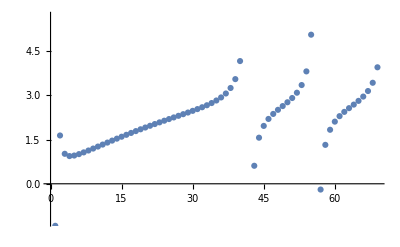

```mathematica
Table[(i Etest[[1,2,i-1]]/Etest[[1,2,i]])//N,{i,2,Length[Etest[[1,2]]]-1}]//ListPlot
```

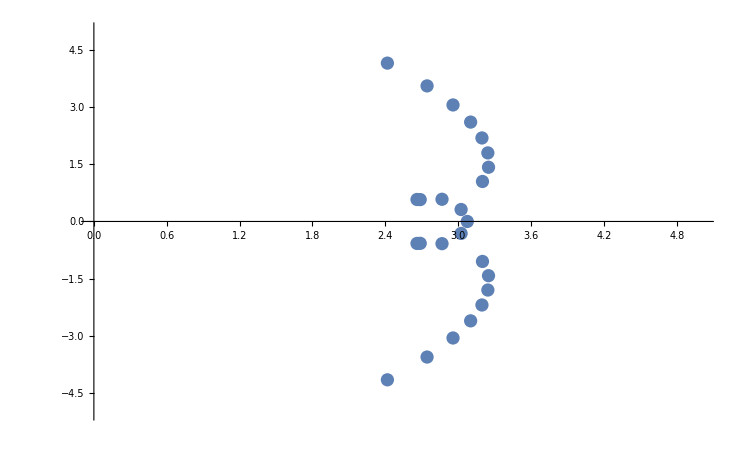

```mathematica
ListPlot[ReIm@s/.Solve[Denominator@PadeApproximant[Sum[(Etest[[1,2]][[i]])/((i)!)s^(i-1),{i,1,Length[Etest[[1,2]]]-1}],{s,0,33}]==0,s],PlotRange->{{0,5},{-5,5}}]
```

## Algebraic curve

```mathematica
((1/2 p^2+Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2+μ2 Sin[x]-u)/.{x->ArcSin[x],p->D[ArcSin[x],x]y})D[ArcSin[x],x]^-2//FullSimplify//Expand//Collect[#,x]&
```

1-u+(-2+u) x^2+x^4+y^2/2+μ0-x^3 μ2+x (μ1+μ2)

```mathematica
(* Compare to the potential I defined *)
Cos[x]^2+(μ0+μ1 Sin[x])/Cos[x]^2+μ2 Sin[x]/.x->π/2+x/.Sin[x]^2->1-Cos[x]^2
```

1+μ2 Cos[x]-Cos[x]^2+(μ0+μ1 Cos[x]) Csc[x]^2

```mathematica
(* So with μ1,μ2==0*)
(* i.e. u->(1-u) and μ0 -> -μ *)
Cos[x]^2+μ0/Cos[x]^2/.x->π/2+x/.Sin[x]^2->1-Cos[x]^2
```

1-Cos[x]^2+μ0 Csc[x]^2

```mathematica
D[ArcSin[x],x]^2
```

1/(1-x^2)

```mathematica
h=Collect[Collect[Collect[Collect[1-u+(-2+u) x^2+x^4+y^2/2+μ0-x^3 μ2+x (μ1+μ2),u],μ0],μ1],μ2]
```

1-2 x^2+x^4+u (-1+x^2)+y^2/2+μ0+x μ1+(x-x^3) μ2

```mathematica
Collect[Collect[Collect[Collect[z^4(h/.{x->x/z,y->y/z^2})//Together,u],μ0],μ1],μ2]//FullSimplify
```

x^4+y^2/2+(-2+u) x^2 z^2+z^4 (1-u+μ0)-x^3 z μ2+x z^3 (μ1+μ2)

```mathematica
Collect[z^4(h/.x->x/z)//Together,μ0]
```

z^4 μ0+1/2 (2 x^4-4 x^2 z^2+2 u x^2 z^2+2 z^4-2 u z^4+y^2 z^4+2 x z^3 μ1-2 x^3 z μ2+2 x z^3 μ2)

```mathematica
D[h,μ1]
```

```mathematica
a[0]-a[1]x
```

```mathematica
num=z^2((2h-y^2-a[0]-a[1]x-a[2]x(1-x^2))/.x->x/z)//Together//FullSimplify
```

2 (-2+u) x^2+(2 x^4)/z^2-z^2 (-2+2 u-2 μ0+a[0])+x z (2 μ1+2 μ2-a[1]-a[2])+(x^3 (-2 μ2+a[2]))/z

```mathematica
PolynomialReduce[num,{(x^2-z^2)},{x,z}]
```

{{(2 x^2+(-2+2 u) z^2+x z (-2 μ2+a[2]))/z^2},2 z^2 μ0+2 x z μ1-z^2 a[0]-x z a[1]}

```mathematica
CoefficientList[2 z^2 μ0+2 x z μ1-z^2 a[0]-x z a[1],{x,z}]
```

{{0,0,2 μ0-a[0]},{0,2 μ1-a[1],0}}

```mathematica
Solve[{(-2 μ2+a[2])==0,2 μ0-a[0]==0,2 μ1-a[1]==0},{a[1],a[2],a[0]}]
```

{{a[1]→2 μ1,a[2]→2 μ2,a[0]→2 μ0}}

```mathematica
(2 x^2+(-2+2 u) z^2)/z^2//Apart
```

2 (-1+u)+(2 x^2)/z^2

```mathematica
RSolve[σ[n,m]==(2n-1)/(m-1)σ[n-1,m-1],σ[n,m],{n,m}]//FullSimplify
```

{{σ[n,m]→(2^n Gamma[1+m-n] Gamma[1/2+n] C[1][-m+n])/(√π Gamma[m])}}

```mathematica
Residue[(√(2h-y^2)//FullSimplify)/(1-x^2),{x,1}]
```

-(√(μ0+μ1))/(√2)

```mathematica
Residue[(√(2h-y^2)//FullSimplify)/(1-x^2),{x,-1}]
```

(√(μ0-μ1))/(√2)

```mathematica
(√(2h-y^2)//FullSimplify)/(1-x^2)/.x->1/x//FullSimplify
```

(x^2 √((2+2 x (-μ2+x (-2+u-u x^2+x (x+x μ0+μ1+μ2))))/x^4))/(-1+x^2)

```mathematica
Residue[(√(2+2 x (-μ2+x (-2+u-u x^2+x (x+x μ0+μ1+μ2)))))/((-1+x^2)x^2),{x,0}]
```

μ2/(√2)

```mathematica
(x^2/√(2h-y^2)//FullSimplify)/.x->1/x//FullSimplify[#,x>0]&
```

1/(√(2+2 x (-μ2+x (-2+u-u x^2+x (x+x μ0+μ1+μ2)))))

```mathematica
Residue[1/(x^2 √(2+2 x (-μ2+x (-2+u-u x^2+x (x+x μ0+μ1+μ2))))),{x,0}]//FullSimplify
```

μ2/(2 √2)